```mathematica
ClearAll["Global`*"];
```

{m[1][0]==-1.87301,x[1][0]==-0.861859,m[2][0]==-1.86163,x[2][0]==1.24721,m[3][0]==-1.03232,x[3][0]==1.97476}

-0.5

0.5

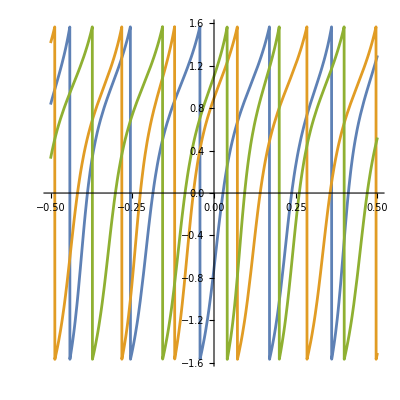

```mathematica
(*Define the system of equations*)
u[k_,t_]:=Apply[Plus,Table[m[j][t]Abs[x[k][t]-x[j][t]],{j,1,n}]]
ux[k_,t_]:=Apply[Plus,Table[m[j][t](x[k][t]-x[j][t])/Abs[x[k][t]-x[j][t]],{j,DeleteCases[Range[1,n],k]}]]

(*Define the number of equations*)
n=3; (*Example for n=5*)

(*Define initial conditions*)
initialConditions=Flatten[Table[{m[i][0]==RandomReal[{-2,2}],x[i][0]==RandomReal[{-2,2}]},{i,n}]]
(*initialConditions={
m[1][t]==1,x[1][t]==t,
m[2][t]==2,x[2][t]==1
};*)

(*Define the system of ODEs*)
eqns=Flatten[Table[{
m[i]'[t]==-m[i][t]ux[i,t]u[i,t],
x[i]'[t]==u[i,t]^2},
{i,n}
]];
(*Solve the system numerically*)
Tstart=-0.5;
Tend=0.5;
T={t,Tstart,Tend};
threshold=10^3;  (*Threshold for wrap-around*)
wrapEvents=Flatten[Table[
With[{i=i},
{
WhenEvent[x[i][t]>threshold,x[i][t]->-threshold+1],
WhenEvent[x[i][t]<-threshold,x[i][t]->threshold-1]
}],{i,n}
]];

sol=NDSolve[Join[eqns,initialConditions,wrapEvents],Flatten[Table[{m[i],x[i]},{i,n}]],T];
Tstart=Apply[Max,Table[sol[[1,i,2]]["Domain"][[1,1]],{i,1,2n}]]
Tend=Apply[Min,Table[sol[[1,i,2]]["Domain"][[1,2]],{i,1,2n}]]
T={t,Tstart,Tend};

XD[i_,t_]=Abs[-m[i][t]ux[i,t]u[i,t]];
Circ[a_,r_]:={r Cos[2ArcTan[a]],r Sin[2ArcTan[a]]};
Circ[a_,r_]:={r Cos[2ArcTan[a]],r Sin[2ArcTan[a]]};

ParametricPlot[Evaluate[Table[{t,ArcTan[x[i][t]]}/.sol[[1]],{i,n}]],{t,Tstart,Tend},AspectRatio->1]
(*pp=ParametricPlot[Evaluate[Table[Circ[x[i][t],XD[i,t]]/.sol[[1]],{i,n}]],{t,Tstart,Tend}]
plotRange1=AbsoluteOptions[pp,PlotRange][[1]][[2]]
plotRange1={{-1,1},{-1,1}};
Manipulate[Graphics[Point[Evaluate[Table[Circ[x[i][d],1]/.sol[[1]],{i,n}]]],Axes->True,PlotRange->plotRange1],{d,Tstart,Tend}]

plotX=Plot[Evaluate[Table[ArcTan[x[i][t]]/. sol,{i,n}]],T,PlotLegends->Table["x["<>ToString[i]<>"]",{i,n}],PlotLabel->"Dynamics of all x[i](t)",PlotStyle->Array[ColorData[97],n]]*)
```

```mathematica
(*Plot all m[i]'s together*)plotM=Plot[Evaluate[Table[m[i][t]/. sol,{i,n}]],T,PlotLegends->Table["m["<>ToString[i]<>"]",{i,n}],PlotLabel->"Dynamics of all m[i](t)",PlotStyle->Array[ColorData[97],n]]

(*Plot all x[i]'s together*)
plotX=Plot[Evaluate[Table[((M2/M1)Tan[M2 t+Pi/4]-x[i][t]+t.5)/. sol,{i,2,2}]],T,PlotLegends->Table["x["<>ToString[i]<>"]",{i,n}],PlotLabel->"Dynamics of all x[i](t)",PlotStyle->Array[ColorData[97],n]]

(*Plot all x[i]'s together*)
plotX=Plot[Evaluate[Table[ArcTan[x[i][t]]/. sol,{i,n}]],T,PlotLegends->Table["x["<>ToString[i]<>"]",{i,n}],PlotLabel->"Dynamics of all x[i](t)",PlotStyle->Array[ColorData[97],n]]

(*Plot all x[i]'s together*)
plotX=Plot[Evaluate[Table[x[i][t]m[i][t]/. sol,{i,n}]],T,PlotLegends->Table["x["<>ToString[i]<>"]",{i,n}],PlotLabel->"Dynamics of all x[i](t)",PlotStyle->Array[ColorData[97],n]]


(*Display the plots*)
GraphicsColumn[{plotM,plotX}];
x[1][Tend]/.sol[[1]];
x[2][Tstart]/.sol[[1]];
```

```mathematica
M1=(m[1][0]m[2][0]Abs[x[2][0]-x[1][0]]+m[1][0]m[3][0]Abs[x[3][0]-x[1][0]]+m[2][0]m[3][0]Abs[x[3][0]-x[2][0]])/.sol[[1]]
M2=(m[1][0]m[2][0]m[3][0])^2Abs[x[2][0]-x[1][0]]Abs[x[3][0]-x[1][0]]Abs[x[3][0]-x[2][0]]/.sol[[1]]
A1=m[1][0]^2(M1+2m[2][0]m[3][0]Abs[x[3][0]-x[2][0]]);
A2=m[2][0]^2(M1+2m[1][0]m[3][0]Abs[x[3][0]-x[1][0]]);
A3=m[3][0]^2(M1+2m[1][0]m[2][0]Abs[x[2][0]-x[1][0]]);
M3A=(A1 x[1][0]^0+A2 x[2][0]^0+A3 x[3][0]^0)/.sol[[1]]
M3B=(A1 x[1][0]^1+A2 x[2][0]^1+A3 x[3][0]^1)/.sol[[1]]
M3C=(A1 x[1][0]^2+A2 x[2][0]^2+A3 x[3][0]^2)/.sol[[1]]
```

55.3245

647.439

5260.79

15760.2

55537.5

```mathematica
118t7.2
```

-29768.6

```mathematica
-2t167.6
```

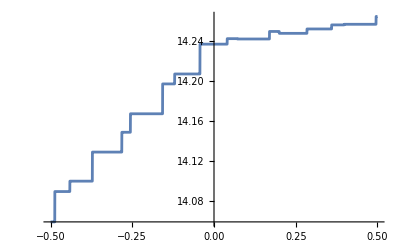

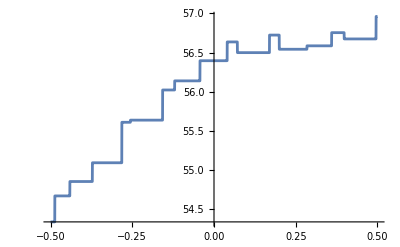

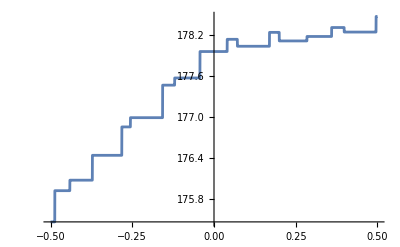

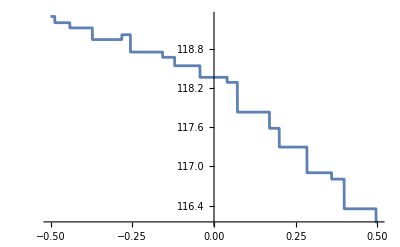

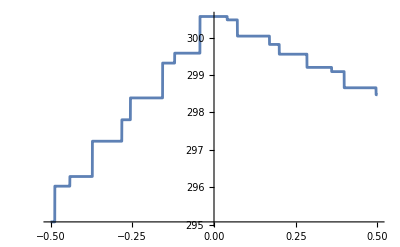

```mathematica
M1=(m[1][t]m[2][t]Abs[x[2][t]-x[1][t]]+m[1][t]m[3][t]Abs[x[3][t]-x[1][t]]+m[2][t]m[3][t]Abs[x[3][t]-x[2][t]])/.sol[[1]];
M2=(m[1][t]m[2][t]m[3][t])^2Abs[x[2][t]-x[1][t]]Abs[x[3][t]-x[1][t]]Abs[x[3][t]-x[2][t]]/.sol[[1]];
A1=m[1][t]^2(M1+2m[2][t]m[3][t]Abs[x[3][t]-x[2][t]]);
A2=m[2][t]^2(M1+2m[1][t]m[3][t]Abs[x[3][t]-x[1][t]]);
A3=m[3][t]^2(M1+2m[1][t]m[2][t]Abs[x[2][t]-x[1][t]]);
M3A=(A1 x[1][t]^0+A2 x[2][t]^0+A3 x[3][t]^0)/.sol[[1]];
M3B=(A1 x[1][t]^1+A2 x[2][t]^1+A3 x[3][t]^1)/.sol[[1]];
M3C=(A1 x[1][t]^2+A2 x[2][t]^2+A3 x[3][t]^2)/.sol[[1]];
plotX=Plot[Evaluate[M1],T]
plotX=Plot[Evaluate[M2],T]
plotX=Plot[Evaluate[M3A],T]
plotX=Plot[Evaluate[M3B],T]
plotX=Plot[Evaluate[M3C],T]
```